### Categorization

Tutorial

EcoEvo Package

EcoEvo`

EcoEvo/tutorial/CompetitionInAPeriodicEnvironment

### Keywords

example

Details

# Competition in a Periodic Environment

This trait-based model considers competition in a variable environment, where an environmental factor such as temperature varies periodically.  Species have a unimodal growth response to temperature, with the optimal temperature, Topt, as an evolvable trait.

where

```mathematica
Needs["EcoEvo`"];
```

Set up model:

```mathematica
SetModel[{Guild[n]->{Equation->dn,Trait[Topt]->{}},Period:>τ}];

dn[i_]:=( μmax E^(-(T[t]-Subscript[Topt, i])^2/σ^2)(1-Sum[Subscript[n, j][t],{j,Nsp[n]}])-d)*Subscript[n, i][t];
T[t]:=15+6 Sin[2π/τ t]; (* temperature *)

τ=365; (* period *)
σ=2.5; (* width of temperature-response curve *)
μmax=3.0; (* maximum growth rate *)
d=0.1; (* death rate *)
```

Plot temperature vs time over one period:

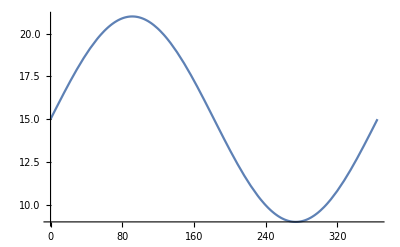

```mathematica
Plot[T[t],{t,0,τ}]
```

Plot invasion rate in the empty environment:

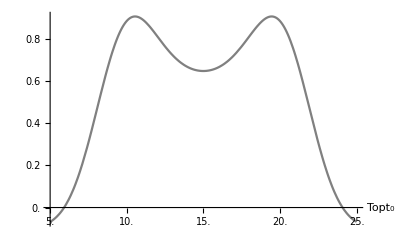

```mathematica
PlotInv[{Subscript[Topt, 0],5,25}]
```

Looks like the underlying fitness landscape is bimodal (due to the sinusoidal forcing).  Let's find (at least one of) the maxima:

```mathematica
MaximizeInv[]
```

{0.904409,{Topt_0→10.5427}}

Now let's simulate the model with a species whose optimum matches the environmental mean (T=15):

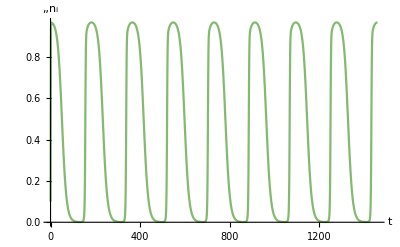

```mathematica
sol=EcoSim[{Subscript[Topt, 1]->15},{Subscript[n, 1]->0.1},4τ];
PlotDynamics[sol]
```

Use the final value as an initial guess to find the limit cycle:

```mathematica
eq=FindEcoCycle[{Subscript[Topt, 1]->15},FinalSlice[sol]]
```

{n_1→InterpolatingFunction[…]}

Now plot the invasion fitness landscape with the resident at Topt=15:

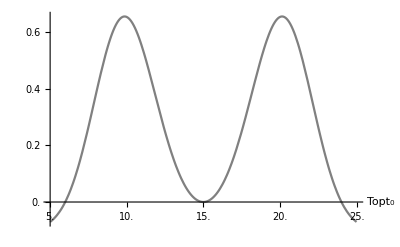

```mathematica
PlotInv[{Subscript[Topt, 1]->15},eq,{Subscript[Topt, 0],5,25}]
```

Looks like a non-ESS at Topt=15.  Let's verify with a PIP:

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {Topt_1→17.1429}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {Topt_1→17.3571}. Trying EcoSim.

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

FindEcoAttractor::novalideq: Couldn't find a valid equilibrium.

FindEcoAttractor::nosteq: Warning: couldn't find a stable equilibrium with traits {Topt_1→9.24107}. Trying EcoSim.

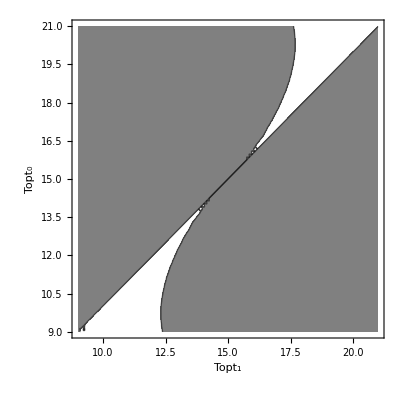

```mathematica
PlotPIP[{Subscript[Topt, 1],9,21},FindEcoAttractorOpts->{TestStability->False}]
```

Looks to be both convergence stable and non-ESS — an evolutionary branching point.  We can simulate the eco-evolutionary dynamics of branching, using a small trait variance to approximate Adaptive Dynamics' separation of time scales:

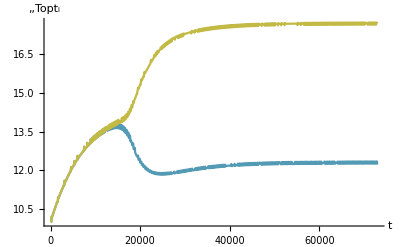

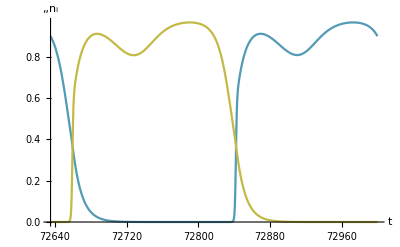

```mathematica
sol=EcoEvoSim[{Subscript[Topt, 1]->10,Subscript[Topt, 2]->10.0001},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{V[Topt]->0.01},200τ];
PlotDynamics[sol,Topt]
PlotDynamics[FinalSlice[sol,τ],n]
```

We can use the final values of this EcoEvoSim as an initial guess for FindEcoCycleEvoEq:

```mathematica
eq2=FindEcoCycleEvoEq[FinalSlice[sol]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{n_1→InterpolatingFunction[…],n_2→InterpolatingFunction[…],Topt_1→12.3114,Topt_2→17.6885}

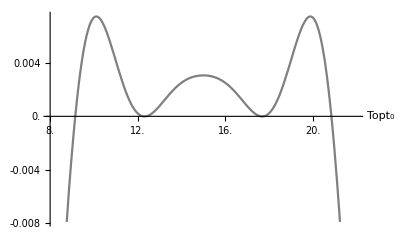

```mathematica
PlotInv[eq2,{Subscript[Topt, 0],8,22}]
```

Not an ESS yet — let's slip in a third species at Topt=15 and follow the eco-evolutionary dynamics:

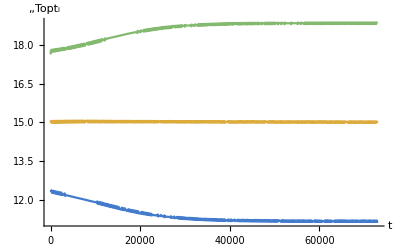

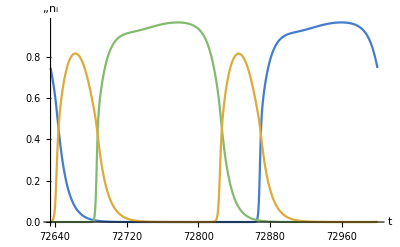

```mathematica
sol=EcoEvoSim[Join[FinalSlice[eq2],{Subscript[Topt, 3]->15,Subscript[n, 3]->0.1}],{V[Topt]->0.01},200τ];
PlotDynamics[sol,Topt]
PlotDynamics[FinalSlice[sol,τ],n]
```

We can again use the final values as initial guesses for FindEcoCycleEvoEq.  We fix the center species at Topt=15 using Fixed, which makes it easier to find the ESS:

```mathematica
eq3=FindEcoCycleEvoEq[FinalSlice[sol],Fixed->{Subscript[Topt, 3]->15}]
```

NDSolve::ndsz: At t == 5.53782, step size is effectively zero; singularity or stiff system suspected.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{n_1→InterpolatingFunction[…],n_2→InterpolatingFunction[…],n_3→InterpolatingFunction[…],Topt_1→11.1766,Topt_2→18.8276,Topt_3→15}

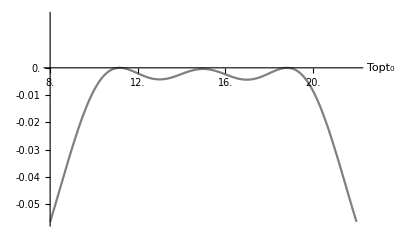

```mathematica
PlotInv[eq3,{Subscript[Topt, 0],8,22}]
```

Finally a global ESS:

```mathematica
GlobalESSQ[eq3]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.29349}. NIntegrate obtained -0.274511 and 1.00128×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.29349}. NIntegrate obtained -0.56956 and 1.02872×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{True},{{-0.000414253,{Topt→14.9889}}}}

The three-species ESS is robust to a little within-species trait variation, but too much results in convergence on a two-species ESS:

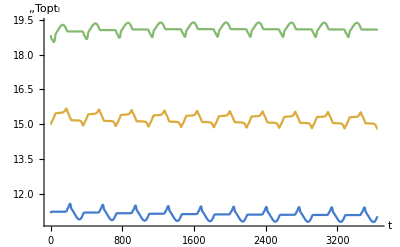

```mathematica
sol=EcoEvoSim[FinalSlice[eq3],{V[Topt]->0.1},10τ];
PlotDynamics[sol,Topt]
```

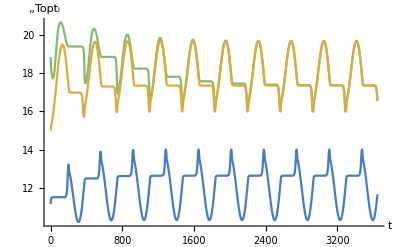

```mathematica
sol=EcoEvoSim[FinalSlice[eq3],{V[Topt]->0.5},10τ];
PlotDynamics[sol,Topt]
```

### References

Kremer CT, Klausmeier CA. 2017. Species packing in eco-evolutionary models of seasonally fluctuating environments. Ecology Letters 20: 1158–1168

More About

Related Tutorials

Related Wolfram Education Group Courses